```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False]
```

# Effect of cooperativity in protein production

Given the minimal model for (fast) protein production, regulated by FB+:

	dx/dt = K + x^n/(1+x^n) - x

corresponding to the following scheme:

-Graphics-

Then we can study the effect of cooperativity term n on the robustness of steady-states towards a fold point. In fact, we can study its effect on the variance and autocorrelation of fluctuations

## Theoretical result, from O-U

By studying perturbations around the mean value of a system approaching a CT, we get the analytical description of their variance, autocorrelation and so on. Here, theoretical result from small alteration of the normal forms.
	Fold: dx/dt = p - Δ x^2
	Transcritical: dx/dt = px - Δ x^2
Summarized in a general k. In this case, noise is additive (and hence the analytical dependence of the variance).

#### Variance

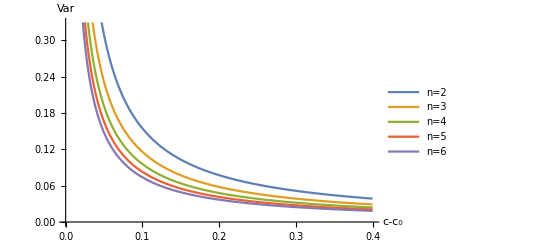

```mathematica
d2=0.01;
x0 = {0.8789,1.2053,1.2804,1.2929,1.2865,1.2741,1.2603};
n={2,3,4,5,6,7,8};
ρ=((x0^n)/(1+x0^n))*1/(2*{0.5208,0.4270,0.3338,0.2686,0.2230,0.1885,0.1640}); 
(* t=\infty; *)
Plot[{(d2/(Sqrt[ρ[[1]]]*k)),(d2/(Sqrt[ρ[[2]]]*k)),(d2/(Sqrt[ρ[[3]]]*k)),(d2/(Sqrt[ρ[[4]]]*k)),(d2/(Sqrt[ρ[[5]]]*k))},{k,0,0.4},AxesLabel->
{Style["c-c_0",18],Style["Var",18]},PlotLegends->Placed[LineLegend[{"n=2","n=3","n=4","n=5","n=6"},LabelStyle->{GrayLevel[0.2],Bold,15},LegendLayout->{"Row",2}],{0.62,0.8}]]
```

Variance as a function of Rho (for any fixed (c-c0))

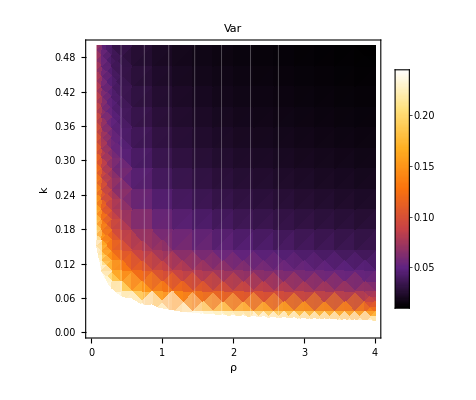

```mathematica
DensityPlot[(d2/(Sqrt[delta]*kei)),{delta,0,4},{kei,0,0.5},PlotLegends->Automatic,FrameLabel->{Style["ρ",20],Style["k",20]},ColorFunction->ColorData["SunsetColors"],PlotLabel->Style["Var",FontSize->20],GridLines->{{{ρ[[1]],Directive[White,Thick]},{ρ[[2]],Directive[White,Thick]},{ρ[[3]],Directive[White,Thick]},{ρ[[4]],Directive[White,Thick]},{ρ[[5]],Directive[White,Thick]},{ρ[[6]],Directive[White,Thick]},{ρ[[7]],Directive[White,Thick]}},None},FrameTicksStyle->Directive[Black,18]]
```

#### Autocorrelation

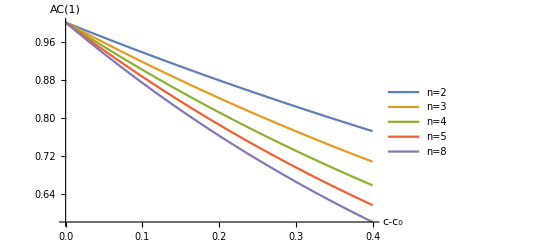

```mathematica
Plot[{Exp[-Sqrt[ρ[[1]]]*k],Exp[-Sqrt[ρ[[2]]]*k],Exp[-Sqrt[ρ[[3]]]*k],Exp[-Sqrt[ρ[[4]]]*k],Exp[-Sqrt[ρ[[5]]]*k]},{k,0,0.4},AxesLabel->
{Style["c-c_0",18],Style["AC(1)",18]},PlotLegends->Placed[LineLegend[{"n=2","n=3","n=4","n=5","n=8"},LabelStyle->{GrayLevel[0.2],Bold,15},LegendLayout->{"Row",2}],{0.67,0.8}]]
```

```mathematica
(* Autocorrelation as a function of Delta (for any fixed (c-c0)) *)
```

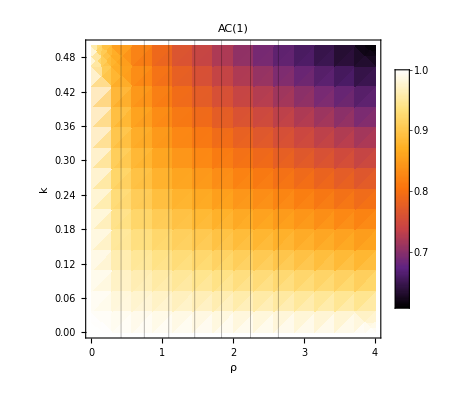

```mathematica
DensityPlot[Exp[-Sqrt[delta]*kei/2],{delta,0,4},{kei,0,0.5},PlotLegends->Automatic,FrameLabel->{Style["ρ",20],Style["k",20]},ColorFunction->ColorData["SunsetColors"],PlotLabel->Style["AC(1)",FontSize->20],GridLines->{{{ρ[[1]],Directive[Black,Thick]},{ρ[[2]],Directive[Black,Thick]},{ρ[[3]],Directive[Black,Thick]},{ρ[[4]],Directive[Black,Thick]},{ρ[[5]],Directive[Black,Thick]},{ρ[[6]],Directive[Black,Thick]},{ρ[[7]],Directive[Black,Thick]}},None},FrameTicksStyle->Directive[Black,18]]
```

## Analytical expressions for stationary probability distribution and stochastic potential of autoc.-FB

### Analytical expression for the stochastic potential

Which is basically the exponent of the probability function but - nicely - does not have normalization constants in the way.

#### Potential depending on changing Hill’s exponent

This is for

```mathematica
0.5*Log[σ]-(1/σ)*∫(k+a*(x^n)/(1+x^n)-x)ⅆx
```

{-(a x+k x-x^2/2-a ArcTan[x])/σ+0.5 Log[σ],-(a x+k x-x^2/2-(a ArcTan[(-1+2 x)/(√3)])/(√3)-1/3 a Log[1+x]+1/6 a Log[1-x+x^2])/σ+0.5 Log[σ],-(a x+k x-x^2/2-(a ArcTan[(-√2+2 x)/(√2)])/(2 √2)-(a ArcTan[(√2+2 x)/(√2)])/(2 √2)+(a Log[1-√2 x+x^2])/(4 √2)-(a Log[1+√2 x+x^2])/(4 √2))/σ+0.5 Log[σ],-1/σ(a x+k x-x^2/2-2/5 √(5/8-(√5)/8) a ArcTan[(1/4 (-1-√5)+x)/(√(5/8-(√5)/8))]-2/5 √(5/8+(√5)/8) a ArcTan[(1/4 (-1+√5)+x)/(√(5/8+(√5)/8))]-1/5 a Log[1+x]+1/20 (1-√5) a Log[1-1/2 (1-√5) x+x^2]+1/20 (1+√5) a Log[1-1/2 (1+√5) x+x^2])+0.5 Log[σ],-(a x+k x-x^2/2+1/6 a ArcTan[√3-2 x]-1/3 a ArcTan[x]-1/6 a ArcTan[√3+2 x]+(a Log[1-√3 x+x^2])/(4 √3)-(a Log[1+√3 x+x^2])/(4 √3))/σ+0.5 Log[σ],0.5 Log[σ]-1/σ(a x+k x-x^2/2-2/7 a ArcTan[Sec[π/14] (x-Sin[π/14])] Cos[π/14]-2/7 a ArcTan[Sec[(3 π)/14] (x+Sin[(3 π)/14])] Cos[(3 π)/14]-1/7 a Log[1+x]+1/7 a Cos[π/7] Log[1+x^2-2 x Cos[π/7]]+1/7 a Log[1+x^2-2 x Sin[π/14]] Sin[π/14]-2/7 a ArcTan[(x-Cos[π/7]) Csc[π/7]] Sin[π/7]-1/7 a Log[1+x^2+2 x Sin[(3 π)/14]] Sin[(3 π)/14]),0.5 Log[σ]-1/σ(a x+k x-x^2/2-1/4 a ArcTan[Sec[π/8] (x-Sin[π/8])] Cos[π/8]-1/4 a ArcTan[Sec[π/8] (x+Sin[π/8])] Cos[π/8]+1/8 a Cos[π/8] Log[1+x^2-2 x Cos[π/8]]-1/8 a Cos[π/8] Log[1+x^2+2 x Cos[π/8]]-1/4 a ArcTan[(x-Cos[π/8]) Csc[π/8]] Sin[π/8]-1/4 a ArcTan[(x+Cos[π/8]) Csc[π/8]] Sin[π/8]+1/8 a Log[1+x^2-2 x Sin[π/8]] Sin[π/8]-1/8 a Log[1+x^2+2 x Sin[π/8]] Sin[π/8])}

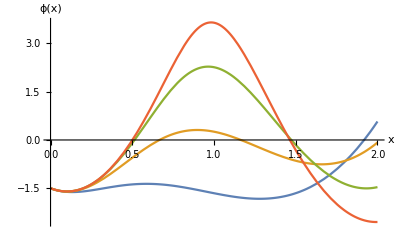

```mathematica
σ=0.05;
k=0.1;
a={1.9};
n={2,3,5,8};
Plot[{-(k x-x^2/2+(a x^(1+n[[1]]) Hypergeometric2F1[1,(1+n[[1]])/n[[1]],1+(1+n[[1]])/n[[1]],-x^n[[1]]])/(1+n[[1]]))/σ+0.5 Log[σ],-(k x-x^2/2+(a x^(1+n[[2]]) Hypergeometric2F1[1,(1+n[[2]])/n[[2]],1+(1+n[[2]])/n[[2]],-x^n[[2]]])/(1+n[[2]]))/σ+0.5 Log[σ],-(k x-x^2/2+(a x^(1+n[[3]]) Hypergeometric2F1[1,(1+n[[3]])/n[[3]],1+(1+n[[3]])/n[[3]],-x^n[[3]]])/(1+n[[3]]))/σ+0.5 Log[σ],-(k x-x^2/2+(a x^(1+n[[4]]) Hypergeometric2F1[1,(1+n[[4]])/n[[4]],1+(1+n[[4]])/n[[4]],-x^n[[4]]])/(1+n[[4]]))/σ+0.5 Log[σ]},{x,0,2},AxesLabel->{Style["x",FontSize->{16}],Style["ϕ(x)",FontSize->{16}]}]
```

### Expression for the probability function

Normalization constants

```mathematica
N1 =NIntegrate[Exp[-(-(k x-x^2/2+(a x^(1+n[[1]]) Hypergeometric2F1[1,(1+n[[1]])/n[[1]],1+(1+n[[1]])/n[[1]],-x^n[[1]]])/(1+n[[1]]))/σ+0.5 Log[σ])],{x,0,3}];
N2 = NIntegrate[Exp[-(-(k x-x^2/2+(a x^(1+n[[2]]) Hypergeometric2F1[1,(1+n[[2]])/n[[2]],1+(1+n[[2]])/n[[2]],-x^n[[2]]])/(1+n[[2]]))/σ+0.5 Log[σ])],{x,0,3}];
N3 = NIntegrate[Exp[-(-(k x-x^2/2+(a x^(1+n[[3]]) Hypergeometric2F1[1,(1+n[[3]])/n[[3]],1+(1+n[[3]])/n[[3]],-x^n[[3]]])/(1+n[[3]]))/σ+0.5 Log[σ])],{x,0,3}];
N4 = NIntegrate[Exp[-(-(k x-x^2/2+(a x^(1+n[[4]]) Hypergeometric2F1[1,(1+n[[4]])/n[[4]],1+(1+n[[4]])/n[[4]],-x^n[[4]]])/(1+n[[4]]))/σ+0.5 Log[σ])],{x,0,3}];
```

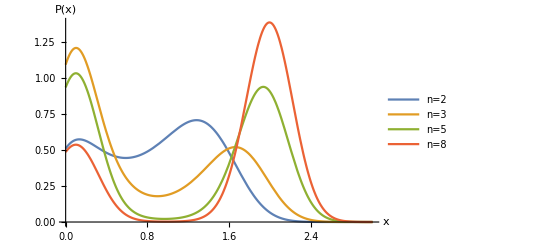

```mathematica
Plot[{(1/N1)*Exp[-(-(k x-x^2/2+(a x^(1+n[[1]]) Hypergeometric2F1[1,(1+n[[1]])/n[[1]],1+(1+n[[1]])/n[[1]],-x^n[[1]]])/(1+n[[1]]))/σ+0.5 Log[σ])],(1/N2)*Exp[-(-(k x-x^2/2+(a x^(1+n[[2]]) Hypergeometric2F1[1,(1+n[[2]])/n[[2]],1+(1+n[[2]])/n[[2]],-x^n[[2]]])/(1+n[[2]]))/σ+0.5 Log[σ])],(1/N3)*Exp[-(-(k x-x^2/2+(a x^(1+n[[3]]) Hypergeometric2F1[1,(1+n[[3]])/n[[3]],1+(1+n[[3]])/n[[3]],-x^n[[3]]])/(1+n[[3]]))/σ+0.5 Log[σ])],(1/N4)*Exp[-(-(k x-x^2/2+(a x^(1+n[[4]]) Hypergeometric2F1[1,(1+n[[4]])/n[[4]],1+(1+n[[4]])/n[[4]],-x^n[[4]]])/(1+n[[4]]))/σ+0.5 Log[σ])]},{x,0,3},PlotLegends->{"n=2","n=3","n=5","n=8"},AxesLabel->{Style["x",FontSize->{16}],Style["P(x)",FontSize->{16}]}]
```

#### Nice plots

```mathematica
Clear[σ,k,a,n]
```

```mathematica
k=0.1;
σ=0.05;
a={1.85,1.85,1.85,1.85}; (* very close to critical value *)
n={2,3,5,8};
ϕ[a_,n_][x_]:=-(k x-x^2/2+(a x^(1+n) Hypergeometric2F1[1,(1+n)/n,1+(1+n)/n,-x^n])/(1+n))/σ+0.5 Log[σ]
P[n_,a_][x_]:=Exp[-(-(k x-x^2/2+(a x^(1+n) Hypergeometric2F1[1,(1+n)/n,1+(1+n)/n,-x^n])/(1+n))/σ+0.5 Log[σ])]
norma[n_,a_][x_]:=NIntegrate[Exp[-(-(k x-x^2/2+(a x^(1+n) Hypergeometric2F1[1,(1+n)/n,1+(1+n)/n,-x^n])/(1+n))/σ+0.5 Log[σ])],{x,0,3}];
```

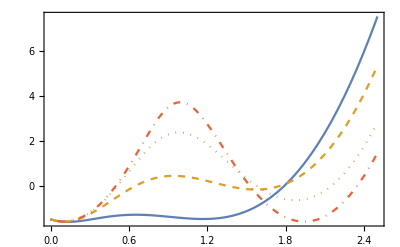

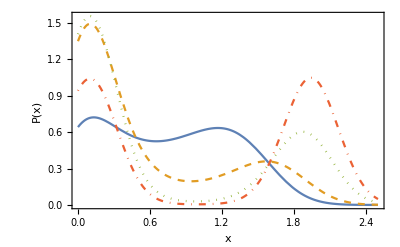

```mathematica
ϕ1=Plot[{ϕ[a[[1]],n[[1]]][x],ϕ[a[[2]],n[[2]]][x],ϕ[a[[3]],n[[3]]][x],ϕ[a[[4]],n[[4]]][x]},{x,0,2.5},Frame->True,PlotStyle->{Line,Dashed,Dotted,DotDashed},FrameTicksStyle->Directive[Black,18]] 
norm1={norma[n[[1]],a[[1]]][x], norma[n[[2]],a[[2]]][x], norma[n[[3]],a[[3]]][x], norma[n[[4]],a[[4]]][x]};
p1=Plot[{P[n[[1]],a[[1]]][x]/norm1[[1]],P[n[[2]],a[[2]]][x]/norm1[[2]],P[n[[3]],a[[3]]][x]/norm1[[3]],P[n[[4]],a[[4]]][x]/norm1[[4]]},{x,0,2.5},Frame->True,PlotStyle->{Line,Dashed,Dotted,DotDashed},AxesLabel->{Style["x",FontSize->16],Style["P(x)",FontSize->16]},FrameTicksStyle->Directive[Black,18]] (*,PlotLegends->{"n=2","n=3","n=5","n=8"}]  *)
```

```mathematica
norm1
```

{6.96943,3.31296,3.17504,4.74645}

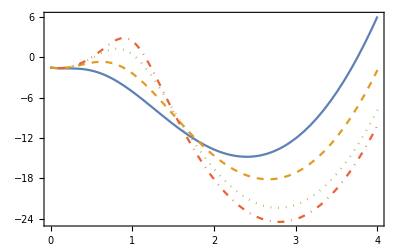

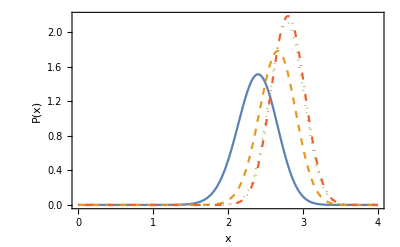

```mathematica
aUp=2.7; (* far from critical value, on upper branch *)
ϕ2=Plot[{ϕ[aUp,n[[1]]][x],ϕ[aUp,n[[2]]][x],ϕ[aUp,n[[3]]][x],ϕ[aUp,n[[4]]][x]},{x,0,4},Frame->True,PlotStyle->{Line,Dashed,Dotted,DotDashed},FrameTicksStyle->Directive[Black,18]] 
norm2=Flatten[{norma[n[[1]],aUp][x], norma[n[[2]],aUp][x], norma[n[[3]],aUp][x], norma[n[[4]],aUp][x]}];
p2=Plot[{P[n[[1]],aUp][x]/norm2[[1]],P[n[[2]],aUp][x]/norm2[[2]],P[n[[3]],aUp][x]/norm2[[3]],P[n[[4]],aUp][x]/norm2[[4]]},{x,0,4},AxesLabel->{Style["x",FontSize->16],Style["P(x)",FontSize->16]},Frame->True,PlotStyle->{Line,Dashed,Dotted,DotDashed},FrameTicksStyle->Directive[Black,18]]
```

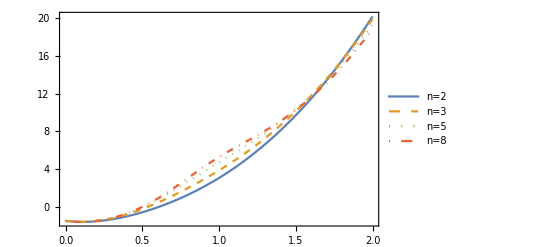

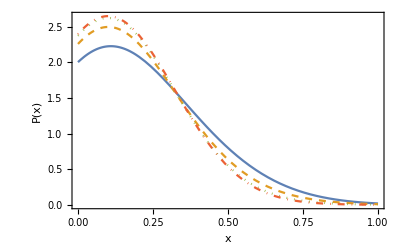

```mathematica
aLow=0.8;
ϕ3=Plot[{ϕ[aLow,n[[1]]][x],ϕ[aLow,n[[2]]][x],ϕ[aLow,n[[3]]][x],ϕ[aLow,n[[4]]][x]},{x,0,2},PlotLegends->Placed[LineLegend[{"n=2","n=3","n=5","n=8"},LabelStyle->{GrayLevel[0.2],25},LegendLayout->{"Row",2}],{0.35,0.75}],Frame->True,PlotStyle->{Line,Dashed,Dotted,DotDashed},FrameTicksStyle->Directive[Black,18]] 
norm3={norma[n[[1]],aLow][x], norma[n[[2]],aLow][x], norma[n[[3]],aLow][x], norma[n[[4]],aLow][x]};
p3=Plot[{P[n[[1]],aLow][x]/norm3[[1]],P[n[[2]],aLow][x]/norm3[[2]],P[n[[3]],aLow][x]/norm3[[3]],P[n[[4]],aLow][x]/norm3[[4]]},{x,0,1},AxesLabel->{Style["x",FontSize->16],Style["P(x)",FontSize->16]},Frame->True,PlotStyle->{Line,Dashed,Dotted,DotDashed},FrameTicksStyle->Directive[Black,18]]
```

#### Excursion rate

For the fold bifurcation, at each n

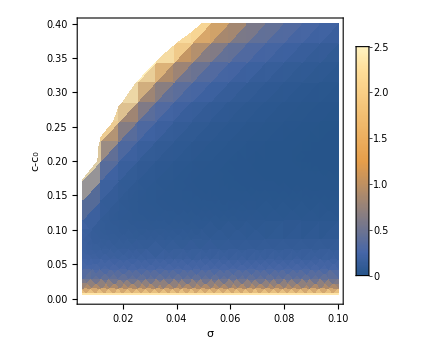
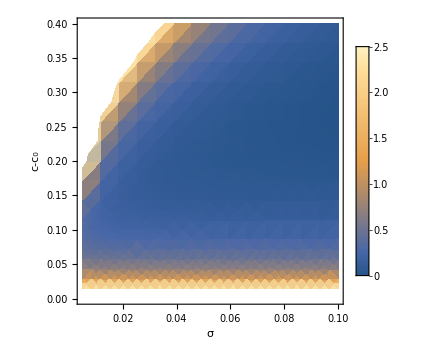
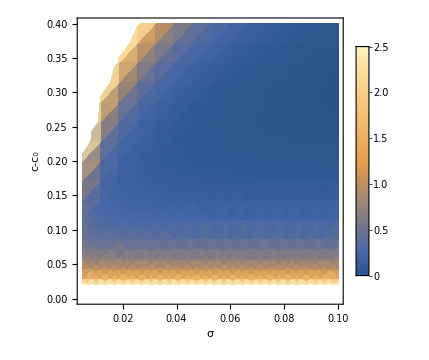
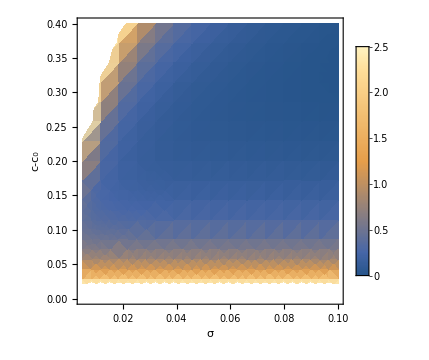

```mathematica
Module[{k,nois,eqs},
eqs={Pi*Exp[(4/3)*k^3/(nois*ρ[[1]])]/(Sqrt[ρ[[1]]]*k),Pi*Exp[(4/3)*k^3/(nois*ρ[[2]])]/(Sqrt[ρ[[2]]]*k),Pi*Exp[(4/3)*k^3/(nois*ρ[[3]])]/(Sqrt[ρ[[3]]]*k),Pi*Exp[(4/3)*k^3/(nois*ρ[[4]])]/(Sqrt[ρ[[4]]]*k)};
Row[DensityPlot[#,{nois,0.005,0.1},{k,0,0.4},ImageSize->Medium,FrameLabel->{Style["σ",18],Style["c-c_0",18]},PlotLegends->Placed[BarLegend[{Automatic,{0,2.5}}],Right]]&/@eqs]]
```

Generic plot

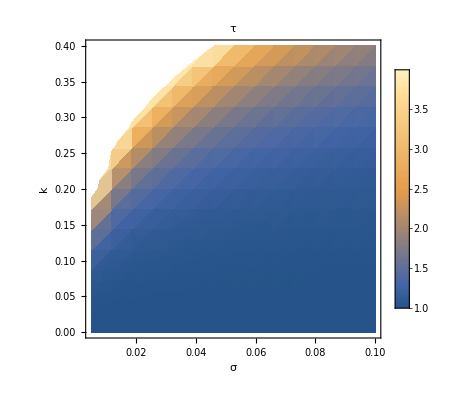

```mathematica
DensityPlot[Exp[(k^(3))/(sigma)],{sigma,0.005,0.1},{k,0,0.4},PlotLegends->Automatic,PlotLabel->Style["τ",FontSize->20],FrameLabel->{Style["σ",18],Style["k",20]},FrameTicksStyle->Directive[Black,18]]
```

#### Supplementary figure

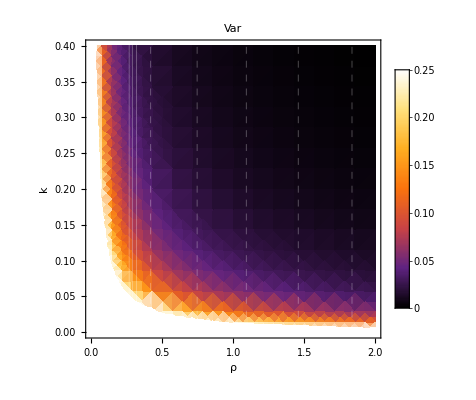

```mathematica
d2=0.01;
x01 = {1.6220,1.4701,1.3019};
diss={3,2.5,2};
ρ1=((x01^2)/(diss+x01^2))*1/(2*{0.8772,0.8032,0.7219});  (*The FW values correspond to diss = [3,2.5,2]. Estimated with equilibria_Other_param_dependencies, n=2 *)
DensityPlot[(d2/(delta*kei)),{delta,0,2},{kei,0,0.4},PlotLegends->Placed[BarLegend[{Automatic,{0,0.25}}],Right],FrameLabel->{Style["ρ",18],Style["k",18]},ColorFunction->ColorData["SunsetColors"],PlotLabel->Style["Var",FontSize->20],GridLines->{{{ρ1[[1]],Directive[White,Thick]},{ρ1[[2]],Directive[White,Thick]},{ρ1[[3]],Directive[White,Thick]},{ρ[[1]],Directive[White,Thick,Dashed]},{ρ[[2]],Directive[White,Thick,Dashed]},{ρ[[3]],Directive[White,Thick,Dashed]},{ρ[[4]],Directive[White,Thick,Dashed]},{ρ[[5]],Directive[White,Thick,Dashed]},{ρ[[6]],Directive[White,Thick,Dashed]},{ρ[[7]],Directive[White,Thick,Dashed]}},None},FrameTicksStyle->Directive[Black,18]]
```